# Pearson’s χ^2 test

Created by © SOUVIK PRIYAM ADHYA, Ph.D.; Post doctoral fellow, Institute of Particle and Nuclear Physics, Charles University, Prague; email : souvikadhya2007@gmail.com

This Mathematica notebook file is free to use and share. An acknowledgement is fine.

#### Initializations :

```mathematica
YOURdpi=2000;
style1a={22,FontFamily->"Times New Roman",FontSlant->Italic};
style1b={22,FontFamily->"Times New Roman",FontSlant->Plain};
style2={AbsoluteThickness[0.9],FontFamily->"Helvetica"};
style1c={14,FontFamily->"Times",FontSlant->Plain};
padding={{50,45},{45,45}};style1c={14,FontFamily->"Times",FontSlant->Plain};
ticks={Directive["Label",12]};
colors="RustTones";
(*colors="RedBlueTones";*)
colors="Rainbow";
sblue=RGBColor[0.13,0.5,0.82](*Customised color define*)
sred =RGBColor[0.94,0.33,0.28](*Customised color define*)
sgreen =RGBColor[0.19,0.67,0.39](*Customised color define*)
scale=Show[ColorData[colors,"Image"],ImageSize->120,Frame->True,FrameTicks->{{None,None},{{{0,0.1},{1,2}},None}}]
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[](*Automatically saves notebook with each execution*)
```

RGBColor[0.13, 0.5, 0.82]

RGBColor[0.94, 0.33, 0.28]

RGBColor[0.19, 0.67, 0.39]

-Graphics-

Objective and procedure :

#### This notebook evaluates the best fit for an OPTIMISED value of parameter from a set of theoretical data with that of experimental data (and/or another dataset). This is achieved by performing goodness of fit by the Pearson’s χ^2 method.

https : // en.wikipedia.org/wiki/Pearson %27 s_chi - squared_test (Wikipedia source for Pearson’s method)

All the datasets used must be mutually exclusive.

What you need a priori ?

First, set the working directory by inserting the path to the data files.

```mathematica
SetDirectory["/Users/souvikpriyamadhya/"];(*Insert the proper path to your working directory*)
```

Example fit to experimental data

Let us fit the data points of ATLAS (LHC) R_AA (any set of points can be fitted with a fitted function this way)

#### Sample experimental data points (with errors):

```mathematica
Needs["ErrorBarPlots`"];
```

```mathematica
(*atlas=Import["/Users/souvikpriyamadhya/atlas.dat"];
atlaserr=Import["/Users/souvikpriyamadhya/atlas_err.dat"];*)(*Uncomment if you want to import your own dataset*)
atlas = {{106.1009,0.4465526},{119.0472,0.4725302},{133.5731,0.4973766},{149.8715,0.5216398},{168.1586,0.5347617},{188.6771,0.5549287},{225.3574,0.5766647},{283.7082,0.5777932},{357.1675,0.6080106},{449.6472,0.5952374},{566.0723,0.580901},{815.4787,0.6053273}};
atlaserr = {{106.1009,0.4465526,0.0006403835},{119.0472,0.4725302,0.0008412191},{133.5731,0.4973766,0.001127383},{149.8715,0.5216398,0.001560896},{168.1586,0.5347617,0.002124222},{188.6771,0.5549287,0.002952138},{225.3574,0.5766647,0.003354065},{283.7082,0.5777932,0.00646074},{357.1675,0.6080106,0.01348369},{449.6472,0.5952374,0.0279633},{566.0723,0.580901,0.0565206},{815.4787,0.6053273,0.1345261}};
```

#### Fitting function for experimental data points :

0.604627-1845.59/x^2.00131

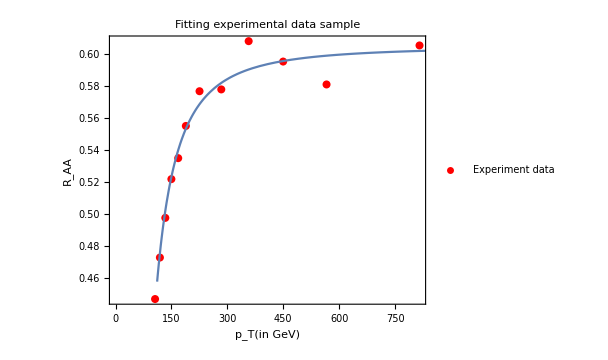

```mathematica
fn[x_]:=a1 x^(-b1)+c1(*Change the function according to the mood of the dataset*)
fitatlas=FindFit[atlas,fn[x],{a1,b1,c1},{x}];
fittedfuncatlas=fn[x]/.fitatlas
Show[ListPlot[atlas,PlotStyle->{Red},PlotLegends->{"Experiment data"}],Plot[fittedfuncatlas,{x,0.,1000.0}],PlotLabel->Style[Framed[  "
Fitting experimental data sample"],14,Black ,Background->Lighter[Yellow]],ImageSize->450,AspectRatio->0.8,
Frame->True,
FrameTicks->True,FrameStyle->style2,
TicksStyle->Automatic,FrameLabel->{Style["p_T(in GeV)",style1b],Style["R_AA",style1b]},
LabelStyle->Directive[FontFamily->"Helvetica",FontSize->14]]
```

Minimisation procedure :

WARNING : This is just a sample dataset which produces a CRUDE optimisation. Use your own (and more) datasets from your theoretical model to generate PRECISE optimisation !

### Datasets (SAMPLE)

#### Experimental dataset from the fitting function

```mathematica
set0atlas=Table[{x,fittedfuncatlas},{x,69.,1000.,19.}]
```

{{69.,0.219126},{88.,0.367697},{107.,0.444411},{126.,0.489112},{145.,0.517418},{164.,0.536465},{183.,0.549892},{202.,0.55971},{221.,0.567106},{240.,0.572815},{259.,0.577314},{278.,0.580922},{297.,0.58386},{316.,0.586284},{335.,0.588307},{354.,0.590013},{373.,0.591465},{392.,0.59271},{411.,0.593787},{430.,0.594725},{449.,0.595546},{468.,0.596268},{487.,0.596908},{506.,0.597478},{525.,0.597986},{544.,0.598442},{563.,0.598853},{582.,0.599224},{601.,0.59956},{620.,0.599866},{639.,0.600145},{658.,0.600401},{677.,0.600635},{696.,0.60085},{715.,0.601048},{734.,0.601231},{753.,0.6014},{772.,0.601557},{791.,0.601703},{810.,0.601839},{829.,0.601965},{848.,0.602083},{867.,0.602194},{886.,0.602297},{905.,0.602394},{924.,0.602485},{943.,0.60257},{962.,0.602651},{981.,0.602727},{1000.,0.602798}}

#### Sample dataset from XYZ theory

```mathematica
setbase={{69.,0.36846730085131396},{88.,0.4145733004840084},{107.,0.4498885359380461},{126.,0.4801160571992583},{145.,0.5064435046821266},{164.,0.529686837423338},{183.,0.5504308303568041},{202.,0.5691089600503559},{221.,0.5860525059372679},{240.,0.601520706774808},{259.,0.6157167846580168},{278.,0.6288076631712475},{297.,0.6409289657494818},{316.,0.6521961837093578},{335.,0.6626997037628988},{354.,0.6725219437760248},{373.,0.6817329545978574},{392.,0.6903871994794382},{411.,0.6985399485461561},{430.,0.7062357079198125},{449.,0.7135123989292056},{468.,0.7204057643194584},{487.,0.7269437387500822},{506.,0.7331600909542242},{525.,0.7390657715085882},{544.,0.7447034567973128},{563.,0.7500805291061824},{582.,0.755214583934708},{601.,0.7601268734045086},{620.,0.7648253162977146},{639.,0.7693285351010353},{658.,0.7736461144543908},{677.,0.7777933438958404},{696.,0.7817768495893187},{715.,0.7856042956976685},{734.,0.7892912257519932},{753.,0.7928429621134919},{772.,0.796266276955472},{791.,0.799563300786086},{810.,0.8027520109629181},{829.,0.8058300854809375},{848.,0.8088036392374577},{867.,0.8116780759173864},{886.,0.814458306681941},{905.,0.8171535427554739},{924.,0.8197636916290413},{943.,0.8222920223536454},{962.,0.8247437314236576},{981.,0.8271217277787751},{1000.,0.8294259816736469}};
```

```mathematica
set1={{69.,0.34800187135535265},{88.,0.4113409776907039},{107.,0.4577970943861208},{126.,0.49382135072432265},{145.,0.5228612456461499},{164.,0.5469435289654041},{183.,0.5672206804572582},{202.,0.5845987669111377},{221.,0.6006781032724123},{240.,0.6156358309718281},{259.,0.6296091779519889},{278.,0.6427104686769365},{297.,0.6550334592504001},{316.,0.6666499724467853},{335.,0.6776332592274934},{354.,0.6880455073866526},{373.,0.6979225483511434},{392.,0.7073184429725318},{411.,0.7162683357975943},{430.,0.7247978225666823},{449.,0.732971100703107},{468.,0.7407779713827679},{487.,0.7482552664987299},{506.,0.7554263706371069},{525.,0.7623072256577734},{544.,0.7689265002214424},{563.,0.7752788695380934},{582.,0.7814036696743555},{601.,0.7872974613936774},{620.,0.7929920815368836},{639.,0.7984802754618424},{658.,0.803780338889412},{677.,0.8089203362288181},{696.,0.8138525908711833},{715.,0.818641865071296},{734.,0.8232798241613772},{753.,0.827777851899936},{772.,0.8321182586685905},{791.,0.8363458043349656},{810.,0.8404390051950917},{829.,0.8444130570568695},{848.,0.8482716152293491},{867.,0.852020489268888},{886.,0.8556634795526662},{905.,0.8592046091889655},{924.,0.862649802129537},{943.,0.8659990903771546},{962.,0.8692565154194072},{981.,0.8724336737730708},{1000.,0.8755252163500015}};
set2={{69.,0.33667070542733857},{88.,0.40134161065924645},{107.,0.448741947866576},{126.,0.48550753866457763},{145.,0.5151370280398387},{164.,0.5397091490938477},{183.,0.5604943499216839},{202.,0.5780960655925079},{221.,0.5941187351356076},{240.,0.6090356911748227},{259.,0.6229771716095747},{278.,0.6360347903772459},{297.,0.648333991180395},{316.,0.6599303166296348},{335.,0.6709044685857674},{354.,0.681295974429781},{373.,0.691169471007093},{392.,0.7005654850910501},{411.,0.7095171336071188},{430.,0.71806117448774},{449.,0.7262432827177632},{468.,0.7340440427124442},{487.,0.7415340928246621},{506.,0.7487178288650842},{525.,0.7556177111140107},{544.,0.7622466996871282},{563.,0.7686322359973364},{582.,0.7747714897204893},{601.,0.7806774843987678},{620.,0.7864024702812333},{639.,0.7919165813519622},{658.,0.7972352877811062},{677.,0.802386760267348},{696.,0.8073675423189395},{715.,0.8121859081343977},{734.,0.816849506062016},{753.,0.821373421815032},{772.,0.8257578285228458},{791.,0.8300076753888596},{810.,0.834132075586886},{829.,0.838141667806834},{848.,0.8420289560398659},{867.,0.8458114158890028},{886.,0.8494871063456972},{905.,0.8530627839211232},{924.,0.856540305959597},{943.,0.8599268040880554},{962.,0.863222961495765},{981.,0.8664288857641697},{1000.,0.8695566267029367}};
set3={{69.,0.30257044451845166},{88.,0.3711865469566823},{107.,0.42149581931672686},{126.,0.460483516332181},{145.,0.49188870050810457},{164.,0.5179206776959999},{183.,0.5399807465602513},{202.,0.5589554994636563},{221.,0.5752651350153899},{240.,0.590039023576556},{259.,0.6038549106905942},{278.,0.616822800658947},{297.,0.6290364539631984},{316.,0.6405715198110715},{335.,0.6514902125306052},{354.,0.6618437351333217},{373.,0.67168712337796},{392.,0.6810602411214766},{411.,0.6900072594772523},{430.,0.6985454778653605},{449.,0.7067204674848192},{468.,0.7145521734711037},{487.,0.7220586613692653},{506.,0.7292688503765123},{525.,0.7362033214216137},{544.,0.7428721983744967},{563.,0.7492950578933586},{582.,0.7554874247356428},{601.,0.7614589526744245},{620.,0.7672251177980873},{639.,0.7727996140292984},{658.,0.778182980569426},{677.,0.7833938827913463},{696.,0.7884331870866723},{715.,0.7933281715203904},{734.,0.7980599894802411},{753.,0.8026617100916099},{772.,0.8071198631622246},{791.,0.8114411973906179},{810.,0.8156536859083738},{829.,0.8197411739230811},{848.,0.8237136811072306},{867.,0.8275847668399378},{886.,0.8313369381646234},{905.,0.8349964462692222},{924.,0.8385645668313734},{943.,0.8420350637458168},{962.,0.8454203004478319},{981.,0.8487207664908307},{1000.,0.8519345228694791}};
set4={{69.,0.28619565260659907},{88.,0.3567168695400226},{107.,0.40841373988464286},{126.,0.4484679935852858},{145.,0.4807231791654676},{164.,0.5074585314318036},{183.,0.5301167215931158},{202.,0.549605646488806},{221.,0.5665782005417141},{240.,0.5813596610453009},{259.,0.5951178561980979},{278.,0.6080371172433339},{297.,0.6202096400085101},{316.,0.631705868679793},{335.,0.6425936512121122},{354.,0.6529262516013443},{373.,0.6627466257901921},{392.,0.6721113551557563},{411.,0.6810419884204868},{430.,0.6895835460897287},{449.,0.6977489271297442},{468.,0.7055826577288381},{487.,0.7130961535673114},{506.,0.7203115391083763},{525.,0.7272384854634208},{544.,0.7339328753499106},{563.,0.7403699936492579},{582.,0.7465757718929611},{601.,0.7525663715980362},{620.,0.7583528860793032},{639.,0.7639431839163849},{658.,0.7693578194750584},{677.,0.7745922246510514},{696.,0.7796571925522785},{715.,0.7845726505551979},{734.,0.7893667433958422},{753.,0.7939617249672245},{772.,0.7984440297840095},{791.,0.802809245717831},{810.,0.8070445133608847},{829.,0.8111670074036481},{848.,0.8151684491214429},{867.,0.8190624369311272},{886.,0.8228593076395305},{905.,0.8265536302693808},{924.,0.8301535004624238},{943.,0.8336584031788934},{962.,0.8370813954708565},{981.,0.8404173845810282},{1000.,0.8436696871455164}};
```

#### Sample parameters from the XYZ theory which gives parameter^optimised

```mathematica
para1=1.;
para2=2.;
para3=3.;
para4=4.;
```

### The MINIMISATION snippet

{chisqr→{0.,0.133092},p-val→{1,1.}}

{chisqr→{0.,0.107423},p-val→{1,1.}}

{chisqr→{0.,0.0561287},p-val→{1,1.}}

{chisqr→{0.,0.0449478},p-val→{1,1.}}

{{1.,0.149729},{2.,0.107423},{3.,0.115378},{4.,0.133092}}

0.211919-0.0792205 x+0.015005 x^2

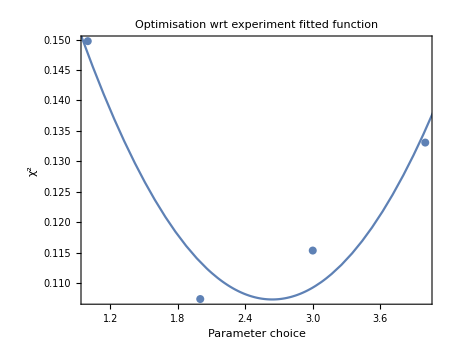

{0.107356,{x→2.6398}}

```mathematica
pearsonTest[obs_List,exp_List]/;Length[obs]==Length[exp]:=Block[{t},t=Total[(obs-exp)^2/exp]//N;
{Rule["chisqr",t],Rule["p-val",SurvivalFunction[ChiSquareDistribution[Length[exp]-1],t]]}]
pearsonTest[set1[[1;;15]],set0atlas[[1;;15]]](*first 15 points taken only, can be increased to all points *)
pearsonTest[set2[[1;;15]],set0atlas[[1;;15]]]
pearsonTest[set3[[1;;15]],set0atlas[[1;;15]]]
pearsonTest[set4[[1;;15]],set0atlas[[1;;15]]]
chipoints={{para1,0.14972875737909921},{para2,0.10742344058509684},{para3,0.11537772418837675},{para4,0.1330924609036162}}
fn[x_]:=a x^2+b x+c
fit1=FindFit[chipoints,fn[x],{a,b,c},{x}];
fittedfunc1=fn[x]/.fit1
Show[ListPlot[chipoints],Plot[fn[x]/.fit1,{x,0.5,5.0}],PlotLabel-> Style[Framed[ "Optimisation wrt experiment fitted function"],14,Black ,Background->Lighter[Yellow]],ImageSize->450,AspectRatio->0.8,
Frame->True,
(*FrameTicks->True,*)FrameStyle->style2,
TicksStyle->Automatic,FrameLabel->{Style["Parameter choice",style1b],Style["χ^2",style1b]},
LabelStyle->Directive[FontFamily->"Helvetica",FontSize->14]]
FindMinimum[fittedfunc1,{x,2.0}]
```

{chisqr→{0.,0.052139},p-val→{1,1.}}

{chisqr→{0.,0.0348564},p-val→{1,1.}}

{chisqr→{0.,0.0274258},p-val→{1,1.}}

{chisqr→{0.,0.0462931},p-val→{1,1.}}

{{1.,0.052139},{2.,0.0348564},{3.,0.0274258},{4.,0.0462931}}

0.0916081-0.0476843 x+0.00903749 x^2

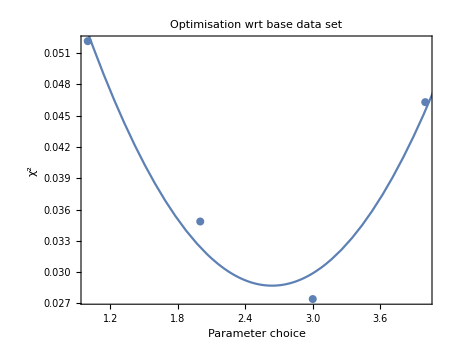

{0.0287093,{x→2.63814}}

```mathematica
pearsonTest[obs_List,exp_List]/;Length[obs]==Length[exp]:=Block[{t},t=Total[(obs-exp)^2/exp]//N;
{Rule["chisqr",t],Rule["p-val",SurvivalFunction[ChiSquareDistribution[Length[exp]-1],t]]}]
pearsonTest[set1[[1;;50]],setbase[[1;;50]]]
pearsonTest[set2[[1;;50]],setbase[[1;;50]]]
pearsonTest[set3[[1;;50]],setbase[[1;;50]]]
pearsonTest[set4[[1;;50]],setbase[[1;;50]]]
chipoints2={{para1,0.052139003238568085},{para2,0.03485637142824487},{para3,0.027425804268033},{para4,0.04629313774520326}}
fn[x_]:=a x^2+b x+c
fit2=FindFit[chipoints2,fn[x],{a,b,c},{x}];
fittedfunc2=fn[x]/.fit2
Show[ListPlot[chipoints2],Plot[fn[x]/.fit2,{x,0.5,5.0}],PlotLabel-> Style[Framed["Optimisation wrt base data set"],14,Black ,Background->Lighter[Yellow]],ImageSize->450,AspectRatio->0.8,
Frame->True,
(*FrameTicks->True,*)FrameStyle->style2,
TicksStyle->Automatic,FrameLabel->{Style["Parameter choice",style1b],Style["χ^2",style1b]},
LabelStyle->Directive[FontFamily->"Helvetica",FontSize->14]]
FindMinimum[fittedfunc2,{x,2.0}]
```

#### Sample datasets generated from XYZ theory for optimizations in parameters

```mathematica
setx2p63opt1={{69.,0.32625373810210695},{88.,0.39209028929494383},{107.,0.44040656500386466},{126.,0.47785163741121095},{145.,0.508025712650864},{164.,0.5330445137849633},{183.,0.554228441423726},{202.,0.5722403094786728},{221.,0.5882078091919071},{240.,0.6030836787805856},{259.,0.6169809681893714},{278.,0.6300204514238142},{297.,0.6422936613067622},{316.,0.6538739733500964},{335.,0.664824060718339},{354.,0.6752229890761552},{373.,0.685079708732264},{392.,0.6944705812570562},{411.,0.7034263730134704},{430.,0.7119670772895274},{449.,0.7201380088759433},{468.,0.7279528907273914},{487.,0.7354583025342922},{506.,0.7426524938272515},{525.,0.7495638748935348},{544.,0.7562104224697799},{563.,0.7626036438803774},{582.,0.7687697990919061},{601.,0.7747045333118175},{620.,0.780432287360109},{639.,0.785966556038743},{658.,0.7913135411926588},{677.,0.7964767668222849},{696.,0.8014848936538441},{715.,0.8063266499700348},{734.,0.8110038476871559},{753.,0.8155649960870077},{772.,0.8199706958478501},{791.,0.8242475629873725},{810.,0.8284098728497891},{829.,0.8324312818298342},{848.,0.8363525241597464},{867.,0.8401582078444032},{886.,0.8438653726679733},{905.,0.8474721842266058},{924.,0.8509775989801834},{943.,0.8543904362562933},{962.,0.8577157625413095},{981.,0.8609555176864513},{1000.,0.8641136118691646}};
setx2p63opt2={{69.,0.38241376307707964},{88.,0.4206696219624374},{107.,0.4523832394061493},{126.,0.47934669321166135},{145.,0.5027033200759794},{164.,0.5232250632942187},{183.,0.5414653786990367},{202.,0.5578315362466959},{221.,0.5726293572407386},{240.,0.5860982174718379},{259.,0.5984304440434502},{278.,0.609776705379176},{297.,0.6202610240394163},{316.,0.6299900463605131},{335.,0.6390473185571298},{354.,0.6475084006870109},{373.,0.6554338143715626},{392.,0.6628765519215474},{411.,0.669882038438542},{430.,0.6764934010151865},{449.,0.6827448606570177},{468.,0.6886668001697277},{487.,0.6942862592230075},{506.,0.699627042083525},{525.,0.7047130992306738},{544.,0.7095579276688169},{563.,0.714184142673445},{582.,0.7186102421898563},{601.,0.7228437366688059},{620.,0.7268988802263994},{639.,0.7307895185073281},{658.,0.7345240782921557},{677.,0.7381155587853551},{696.,0.7415685779366457},{715.,0.7448937633341512},{734.,0.7481019079444303},{753.,0.7511929755980334},{772.,0.7541753358218459},{791.,0.7570598898736195},{810.,0.7598458141213036},{829.,0.7625397161082227},{848.,0.7651434397790178},{867.,0.7676765569974972},{886.,0.7701239316021364},{905.,0.7724991086132044},{924.,0.7747992564143904},{943.,0.777035310861447},{962.,0.7792068547386617},{981.,0.7813171100364691},{1000.,0.7833687969570354}};
```

Plotting the final output for the optimised parameters from XYZ theory.

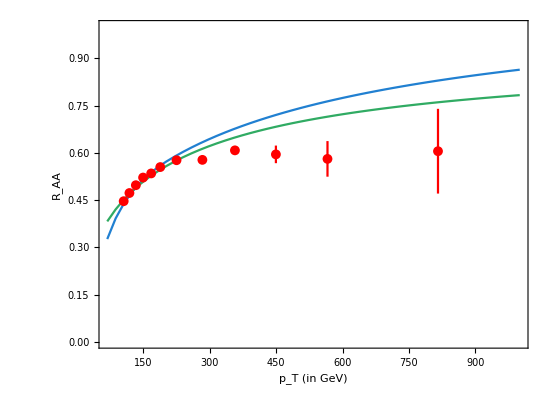

```mathematica
figtheoryvsexpt=Show[ListPlot[{setx2p63opt1,setx2p63opt2},ImageSize->550,AspectRatio->0.75,
PlotStyle->{{sblue},{sgreen}},Joined-> True,PlotRange->{All,{0.,1.0}},PlotLegends->Placed[{"Optimised wrt experimental data fit function","Optimised wrt sample base data"},{Right,Bottom}],
Frame->True,TicksStyle->Automatic,AxesStyle->Medium,FrameStyle->Medium,
FrameLabel->{Style["p_T (in GeV)",style1b],Style["R_AA",style1b]},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->14]],ErrorListPlot[{{#1,#2},ErrorBarPlots`ErrorBar@@{#3}}&@@@atlas2,PlotRangePadding->{Scaled[0.15],Automatic},PlotStyle->{Red},PlotLegends->Placed[{"ATLAS R_AA"},{Right,Bottom}]]]
(*Export[ToString[StringForm["/Users/souvikpriyamadhya/figtheoryvsexpt.pdf",$UserName]],figtheoryvsexpt];*)(*Uncomment if you want to export your file in pdf/jpeg format*)
```

## That’s all folks !